## Estimate Standard Map Distribution

### Introduction

Estimation of the distribution of data from the Standard Map
Data comes from Tirnakli, Ugur, and Ernesto P. Borges. 2015. “The Standard Map: From Boltzmann-Gibbs Statistics to Tsallis Statistics.” Statistical Mechanics. Nature Publishing Group arXiv: 150 (January): 2–9. https://doi.org/10.1038/srep23644.

-Graphics-

Definition of the coupled Gaussian for this data.
1/Z Exp_κ^(-1/2)[(x/σ)^2]=1/Z(1+(κ(x/σ))^2)^(-κ/(2(1+κ)))
Z = 1/(P(0))=1/0.0363=27.5
κ = (-(1 - q))/(2 + (1 - q)) =0.935/(2-0.935)=0.878
Although the paper does not explicitly specify beta, which is the inverse square root of the scale, the scale can be determined from Z and κ.  The papers published value for P(0) was in error.  0.0363 was revised to be 3.297. See the section “Revised Tirnakli Estimate”.

```mathematica
σ=(Z √κ Gamma[(1+κ)/(2κ)])/(√π Gamma[1/(2κ)])/.{Z->27.5,κ->0.878}
```

8.96657

f(0) = (√κ)/(σ B(1/(2κ),1/2)); σ = (√κ)/(f(0) B(1/(2κ),1/2))

```mathematica
σ=(√κ)/(f0 Beta[1/(2κ),0.5])/.{f0->0.0363,κ->0.878}
```

8.98229

```mathematica
1/0.0363
```

27.5482

### Case K=0.0

#### Import Dataset, K = 0.0

```mathematica
fileName=SystemDialogInput["FileOpen"]
```

/Users/kenricnelson/Documents/Wolfram Mathematica/Estimation/Standard Map Data & Code/sumx-K0-T4194304-ini200M-Tpi-div2pi-divlnT

```mathematica
(*Close[stream];*)
stream = OpenRead[fileName];
```

```mathematica
standardMapData=ReadList[stream,Number,2 10^8];
Length[standardMapData]
```

200000000

#### Estimate Distribution, K = 0.0

```mathematica
(* Compute and organize data *)
segLength=200000000; numSegments = Length[standardMapData]/segLength;
estimates=Table[EstimateCoupledDistribution[standardMapData⟦(i-1)segLength+1;;i segLength⟧,
"iterations"-><|"iterateXeqX"->1,"iterateRec"->2|>, (* IA 2000 Paper: 10 & 20 *)  
"sampleRange"->0.1,(* IA 2000 Paper: 0.1*)  
"cloudQ"->False],
{i, 1,numSegments,numSegments}
]
```

Mean: 0.0005140.000035  Scale: 0.0775397  Coupling: 0.878370.00013

{{<|lowestVariability→{0.0005140.000035,11012768},lowestVarNearEnd→{0.0005140.000035,11012768},firstLast→{{0.00050.0005,5508528},{0.0005140.000035,11012768}},minMax→{{0.00050.0005},{0.0005140.000035}},sampleRange→0.1,allEst→{0.000488954,0.000538686},allCombinedEsts→{{0.00050.0005,5508528},{0.0005140.000035,11012768}},XeqX→{}|>,<|lowestVariability→{0.0775397,1726053},lowestVarNearEnd→{0.0775397,1726053},firstLast→{0.080.08,0.0775397},minMax→{{0.0775397},{0.080.08}},sampleRange→0.1,allEst→{0.0775444,0.0775344},allCombinedEsts→{{0.080.08,863417},{0.0775397,1726053}},XeqX→{}|>,{{0.878284,0.878464},0.878370.00013}}}

```mathematica
Save["/Users/kenricnelson/Documents/Wolfram Mathematica/Estimation/Standard Map Data & Code/SM_DistEst_whole_200mleng_K0-0",estimates]
```

```mathematica
couplingToq[0.878370.00013]
```

1.935250.00015

```mathematica
scaleToBeta[0.0775397,2]
```

166.3240.030

#### Evaluate Distribution Fit, K = 0.0

```mathematica
hypothesisTest = DistributionFitTest[standardMapData,
StudentTDistribution[ 0.000514, 0.07753,1/0.87837],{"CramerVonMises","TestDataTable"}]
```

{8.31557×10^-14, | Statistic | P-Value
Cramér-von Mises | 10213. | 8.31557×10^-14}

```mathematica
estimatedDistML = EstimatedDistribution[standardMapData,
StudentTDistribution[μ, σ, ν],
ParameterEstimator->"MaximumLikelihood"]
hypothesisTestML = DistributionFitTest[standardMapData⟦1;;segLength⟧,
estimatedDistML,{"CramerVonMises","TestDataTable"}]
```

StudentTDistribution[9.33736×10^-6,0.0800404,1.11707]

{5.62883×10^-14, | Statistic | P-Value
Cramér-von Mises | 5210.92 | 5.62883×10^-14}

#### Hill Estimator for Tail, K = 0.0

```mathematica
n=200000000;
x=standardMapData;
x=Sort[x,Greater];
κ=Table[{k,Mean[Log[x[[1;;k-1]]]-Log[x[[k]]]]},{k,1000000,2000000}];
ListPlot[κ,AxesLabel->(Style[#,18,Italic,Bold]&)/@{"k","κ"},Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
Mean[κ⟦120000;;160000,2⟧]
```

```mathematica
Mean[κ]
```

{1500000,0.920646}

```mathematica
estimatedDistML = EstimatedDistribution[standardMapData,
StudentTDistribution[μ, σ, 1/0.92],
ParameterEstimator->"MaximumLikelihood"]
hypothesisTestML = DistributionFitTest[standardMapData⟦1;;segLength⟧,
estimatedDistML,{"CramerVonMises","TestDataTable"}]
```

StudentTDistribution[9.34623×10^-6,0.079045,1.08696]

{5.36238×10^-14, | Statistic | P-Value
Cramér-von Mises | 4959.3 | 5.36238×10^-14}

```mathematica
estimatedDistTir = EstimatedDistribution[standardMapData,
StudentTDistribution[0,8.97, 0.878],
ParameterEstimator->"MaximumLikelihood"]
hypothesisTestTir = DistributionFitTest[standardMapData⟦1;;segLength⟧,
estimatedDistTir,{"CramerVonMises","TestDataTable"}]
```

StudentTDistribution[0,8.97,0.878]

{8.67861×10^-13, | Statistic | P-Value
Cramér-von Mises | 770069. | 8.67861×10^-13}

#### Rerun Cramer von Mises on Full Dataset

```mathematica
Monitor[CramerVonMisesTest[standardMapData,#],#]&/@
{StudentTDistribution[5.14 10^-4,0.0775,1/0.878],
StudentTDistribution[9.34 10^-6,0.0800,1/0.893],
StudentTDistribution[9.35 10^-6,0.0790,1/0.926],
StudentTDistribution[0,8.97,1/0.878]}
```

{8.65974×10^-14,5.75096×10^-14,5.42899×10^-14,4.02323×10^-12}

Rerun CVM Test with revised Tirnakli estimate

```mathematica
CramerVonMisesTest[standardMapData,StudentTDistribution[0,0.0989,1/0.878]]
```

3.19522×10^-13

#### Evaluate LogLikelihood of estimates

```mathematica
Monitor[LogLikelihood[#,standardMapData],#]&/@
{StudentTDistribution[5.14 10^-4,0.0775,1/0.878],
StudentTDistribution[9.34 10^-6,0.0800,1/0.893],
StudentTDistribution[9.35 10^-6,0.0790,1/0.926],
StudentTDistribution[0,8.97,1/0.878]}
```

{2.27334×10^7,2.28397×10^7,2.2807×10^7,-6.65128×10^8}

```mathematica
{2.2733404654464483*^7,2.2839736270891488*^7,2.2806984065855205*^7,-6.65127870325366*^8}/(2 10^8)
```

{0.113667,0.114199,0.114035,-3.32564}

Rerun LogLikelihood with revised Tirnakli estimate

```mathematica
LogLikelihood[StudentTDistribution[0,0.0989,1/0.878],standardMapData]
```

2.06412×10^7

#### Evaluate Middle Domain

```mathematica
standardMapDataMiddle=Select[standardMapData,0.001<=#<=1000&];
```

```mathematica
Monitor[CramerVonMisesTest[standardMapDataMiddle,#],#]&/@
{StudentTDistribution[5.14 10^-4,0.0775,1/0.878],
StudentTDistribution[9.34 10^-6,0.0800,1/0.893],
StudentTDistribution[9.35 10^-6,0.0790,1/0.926],
StudentTDistribution[0,8.97,1/0.878]}
```

{3.01348×10^-12,2.97873×10^-12,2.98062×10^-12,2.79188×10^-12}

```mathematica
Rerun CVM Test with revised Tirnakli estimate
```

```mathematica
CramerVonMisesTest[standardMapDataMiddle,StudentTDistribution[0,0.0989,1/0.878]]
```

2.77967×10^-12

```mathematica
Monitor[LogLikelihood[#,standardMapDataMiddle],#]&/@
{StudentTDistribution[5.14 10^-4,0.0775,1/0.878],
StudentTDistribution[9.34 10^-6,0.0800,1/0.893],
StudentTDistribution[9.35 10^-6,0.0790,1/0.926],
StudentTDistribution[0,8.97,1/0.878]}
```

{7.81955×10^6,7.55132×10^6,7.51756×10^6,-3.23305×10^8}

```mathematica
%13/(2 10^8)
```

{0.0390978,0.0377566,0.0375878,-1.61653}

```mathematica
Rerun LogLikelihood with revised Tirnakli estimate
```

```mathematica
LogLikelihood[StudentTDistribution[0,0.0989,1/0.878],standardMapDataMiddle]/(2 10^8)
```

0.035142

#### Summary of Results for first 10,000,000

```mathematica
TableForm[{{0,8.97,0.878,0.0363,scaleShapeToBeta[8.97,0.878],couplingToq[0.878], 8.67 10^-13 },
{0,0.0989,0.878,3.30,scaleShapeToBeta[0.0989,0.878],couplingToq[0.878], "Not Recorded" },
{8.59 10^-5,0.0801,1/1.12,1/NormCG[0.0801,1/1.12],scaleShapeToBeta[0.0801,1/1.12], couplingToq[1/1.12], 7.77 10^-15},
{8.57 10^-5,0.0788,1/1.08,1/NormCG[0.0788,1/1.08],scaleShapeToBeta[0.0788,1/1.08], couplingToq[1/1.08], 4.33 10^-15},
{6.87 10^-4,0.0771,0.898,1/NormCG[0.0771,0.989],scaleShapeToBeta[0.0771,0.898], couplingToq[0.898],1.07 10^-14}},
TableHeadings->{{"Tirnakli Report","Tirnakli Revision","Max Likelihood", "Hill & ML","Indep. Approx."}, {"Location", "Scale", "Shape", "P(0)","Beta", "q", "Cramer-von Mises"}}
]
```

| Location | Scale | Shape | P(0) | Beta | q | Cramer-von Mises
Tirnakli Report | 0 | 8.97 | 0.878 | 0.0363 | 0.0116703 | 1.93504 | 8.67×10^-13
Tirnakli Revision | 0 | 0.0989 | 0.878 | 3.3 | 96.0004 | 1.93504 | Not Recorded
Max Likelihood | 0.0000859 | 0.0801 | 0.892857 | 4.05851 | 147.51 | 1.9434 | 7.77×10^-15
Hill & ML | 0.0000857 | 0.0788 | 0.925926 | 4.0984 | 155.08 | 1.96154 | 4.33×10^-15
Indep. Approx. | 0.000687 | 0.0771 | 0.898 | 4.13733 | 159.646 | 1.94626 | 1.07×10^-14

#### Summary of Results for full 200,000,000

```mathematica
estimates[[1,1]]["allCombinedEsts"]⟦2,1⟧//FullForm
```

Around[0.000686983,0.000482946]

```mathematica
estimates[[1,2]]["allCombinedEsts"]⟦2,1⟧//FullForm
```

Around[0.0770929,0.0000251155]

```mathematica
TableForm[{{0,8.97,0.878,0.0363,scaleShapeToBeta[8.97],couplingToq[0.878], 8.67 10^-13 },
{0,0.0989,0.878,3.30,scaleShapeToBeta[0.0989,0.878],couplingToq[0.878], 3.20 10^-13 },
{9.34*^-6,0.0800,1/1.12,1/NormCG[0.0800,1/1.12],scaleShapeToBeta[0.0800], couplingToq[1/1.12], 5.63*^-14},
{9.35*^-6,0.0790,1/1.08,1/NormCG[0.0790,1/1.08],scaleShapeToBeta[0.0790], couplingToq[1/1.08], 5.36*^-14},
{0.000514, 0.0775,0.87837,1/NormCG[0.0775,0.878],scaleShapeToBeta[0.0775], couplingToq[0.878],8.32*^-14}},
TableHeadings->{{"Tirnakli Report","Tirnakli Revision","Max Likelihood", "Hill & ML","Indep. Approx."}, {"Location", "Scale", "Shape", "P(0)","Beta", "q", "Cramer-von Mises"}}
]
```

| Location | Scale | Shape | P(0) | Beta | q | Cramer-von Mises
Tirnakli Report | 0 | 8.97 | 0.878 | 0.0363 | scaleShapeToBeta[8.97] | 1.93504 | 8.67×10^-13
Tirnakli Revision | 0 | 0.0989 | 0.878 | 3.3 | 96.0004 | 1.93504 | 3.2×10^-13
Max Likelihood | 9.34×10^-6 | 0.08 | 0.892857 | 4.06358 | scaleShapeToBeta[0.08] | 1.9434 | 5.63×10^-14
Hill & ML | 9.35×10^-6 | 0.079 | 0.925926 | 4.08802 | scaleShapeToBeta[0.079] | 1.96154 | 5.36×10^-14
Indep. Approx. | 0.000514 | 0.0775 | 0.87837 | 4.20719 | scaleShapeToBeta[0.0775] | 1.93504 | 8.32×10^-14

#### Histogram and Distribution Estimates Graph

```mathematica
fileName=SystemDialogInput["FileOpen"]
```

/Users/kenricnelson/Documents/Wolfram Mathematica/Estimation/Standard Map Data & Code/sumx-K0-T4194304-ini200M-Tpi-div2pi-divlnT

```mathematica
(*Close[stream];*)
stream = OpenRead[fileName];
```

```mathematica
standardMapData=ReadList[stream,Number,2 10^8];
SMLength=Length[standardMapData]
```

200000000

```mathematica
centeredBy=5.14 10^-4;
standardMapCentered=Select[standardMapData-centeredBy,#>0&];
```

```mathematica
centeredBy=5.14 10^-4;
standardMapCentered=Abs[standardMapData-centeredBy];
```

```mathematica
TickCustom={{{10^-9,"10^-9",{0,0.02}},{10^-8,"",{0,0.02}},{10^-7,"",{0,0.02}},{10^-6,"10^-6",{0,0.02}},{10^-5,"",{0,0.02}},{10^-4,"",{0,0.02}},{10^-3,"10^-3",{0,0.02}},{10^-2,"",{0,0.02}},{10^-1,"",{0,0.02}},{1,"1",{0,0.02}},{10,"",{0,0.02}},{10^2,"",{0,0.02}},{10^3,"10^3",{0,0.02}},{10^4,"",{0,0.02}},{10^5,"",{0,0.02}}},{{10^-12,"10^-12"},{10^-11,""},{10^-10,""},{10^-9,"10^-9"},{10^-8,""},{10^-7,""},{10^-6,"10^-6"},{10^-5,""},{10^-4,""},{10^-3,"10^-3"},{10^-2,""},{10^-1,""},{1,"1"},{10,""},{10^2,""},{10^3,"10^3"},{10^4,""},{10^5,""},{10^6,"10^6"}}};standardMapHistogram=Histogram[standardMapCentered,"Log",{"Log","PDF"},Ticks->TickCustom,ChartBaseStyle->Directive[LightCyan]];
```

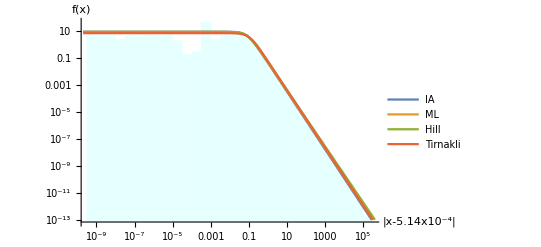

```mathematica
Show[standardMapHistogram,
LogLogPlot[{
2PDF[StudentTDistribution[5.14 10^-4-centeredBy,0.0775,1/0.878],x],
2PDF[StudentTDistribution[9.34 10^-6-centeredBy,0.0800,1/0.893],x],
2PDF[StudentTDistribution[9.35 10^-6-centeredBy,0.0790,1/0.926],x],
2PDF[StudentTDistribution[0,0.0989,1/0.878],x]
},{x,2 10^-10,10^6},
PlotLegends->Placed[{"IA","ML","Hill","Tirnakli"},Right],
PlotRange->{{10^-8,10^5},{10^-13,100}},
AxesOrigin->{2 10^-10,10^-13},
Ticks->TickCustom
],
AxesStyle->Bold,
AxesLabel->{Style["|x-5.14x10^-4|",Bold],Style["f(x)",Bold]},
Epilog->Inset[LogPlot[{
2PDF[StudentTDistribution[5.14 10^-4,0.0775,1/0.878],x],
2PDF[StudentTDistribution[9.34 10^-6,0.0800,1/0.893],x],
2PDF[StudentTDistribution[9.35 10^-6,0.0790,1/0.926],x],
2PDF[StudentTDistribution[0,0.0989,1/0.878],x]
},{x,7.2 10^3,9.8 10^3},
Ticks->{{{8000,"8000"},{9000,"9000"}},
{{ 2 10^-10,"2x10^-10"},{4 10^-10,"4x10^-10"}}},
PlotRegion->{{0,0.6},{0,0.6}},
AspectRatio->1.
],
{10,0}]
]
```

#### Saved Results

With 10^6 Samples; no adjustment of axes

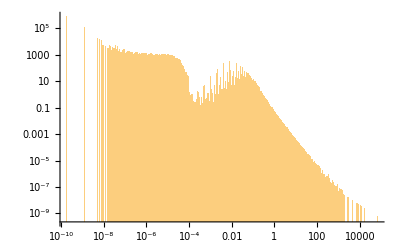

```mathematica
Histogram[Abs[standardMapData],{"Log","Wand"},{"Log","PDF"}]
```

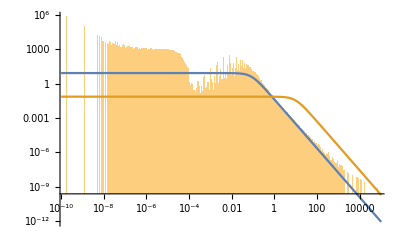

```mathematica
Show[%29,
LogLogPlot[{2PDF[StudentTDistribution[0,0.0775,1/0.878],x],
2PDF[StudentTDistribution[0,8.97,1/0.878],x]},
{x,10^-10,10^5}]]
```

For Tirnakli plot is Linear-Log with scaling by P(0),  {y P(0), P(y)/P(0)}; 
        P(0) = 0.0363

without scaling of axes

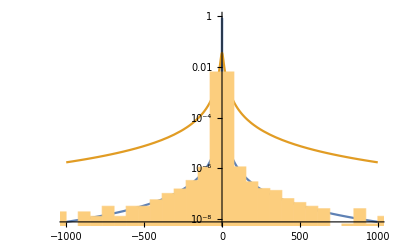

```mathematica
Show[
LogPlot[{PDF[StudentTDistribution[0,0.0775,1/0.878],x],
PDF[StudentTDistribution[0,8.97,1/0.878],x]},
{x,-10^4,10^4}],
Histogram[standardMapData,Automatic,{"Log","PDF"}]]
```

With 10^8 Samples

```mathematica
Show[Histogram[Abs[standardMapData],{"Log","Wand"},{"Log","PDF"}],
2LogLogPlot[{PDF[StudentTDistribution[0,0.0775,1/0.878],x],
2PDF[StudentTDistribution[0,8.97,1/0.878],x]},
{x,10^-10,10^5}]]
```

-Graphics-

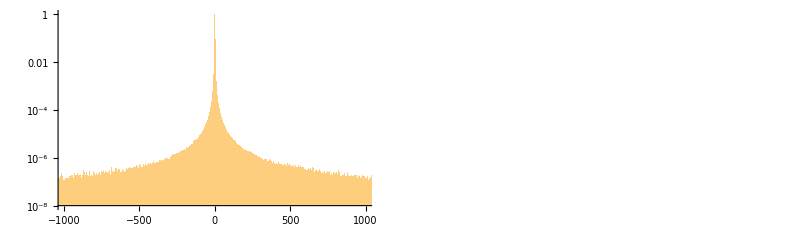

```mathematica
GraphicsRow[{Show[
Histogram[standardMapData*P0IA,{0.2},scaleCountP0IA,
PlotRange->{{-1000,1000},Automatic},
ScalingFunctions->"Log"],
Plot[PDF[StudentTDistribution[0,0.0775,1/0.878],x/P0IA]/P0IA ,{x,-1000,1000 },
ScalingFunctions->"Log",
PlotRange->{{-1000,1000},{10^-8,1}}]],
Show[
Histogram[standardMapData*P0TR,{0.2},scaleCountP0TR,
PlotRange->{{-1000,1000},Automatic},
ScalingFunctions->"Log"],
Plot[PDF[StudentTDistribution[0,8.975,1/0.878],x/P0TR] /P0TR,{x,-1000 ,1000},
ScalingFunctions->"Log",
PlotRange->{{-1000,1000},{10^-8,1}}]
]
}]
```

Attempts to Match Histogram and PDF according to Tirnakli results

```mathematica
maxCount=Max[%35];
```

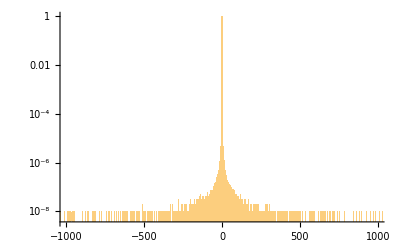

```mathematica
scaleCount[bins_,counts_]:=counts/maxCount;Histogram[standardMapData*P0TR,{0.2},scaleCount,
PlotRange->{{-1000,1000},Automatic},
ScalingFunctions->"Log"]
```

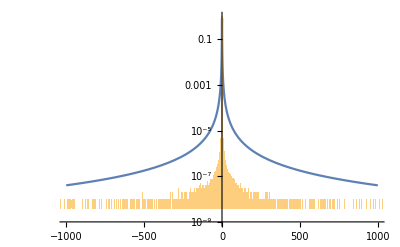

```mathematica
Show[Plot[PDF[StudentTDistribution[0,8.975,1/0.878],x/P0TR] /P0TR,{x,-1000,1000},
ScalingFunctions->"Log",
PlotRange->{{-1000,1000},{10^-9,1}}],
%38]
```

```mathematica
TickCustom={{{10^-9,"10^-9"},{10^-8,""},{10^-7,""},{10^-6,"10^-6"},{10^-5,""},{10^-4,""},{10^-3,"10^-3"},{10^-2,""},{10^-1,""},{1,"1"},{10,""},{10^2,""},{10^3,"10^3"},{10^4,""},{10^5,""}},{{10^-10,""},{10^-9,"10^-9"},{10^-8,""},{10^-7,""},{10^-6,"10^-6"},{10^-5,""},{10^-4,""},{10^-3,"10^-3"},{10^-2,""},{10^-1,""},{1,"1"},{10,""},{10^2,""},{10^3,"10^3"},{10^4,""},{10^5,""},{10^6,"10^6"}}};
Show[Histogram[Abs[standardMapData],{"Log","Wand"},{"Log","PDF"},
Ticks->TickCustom],
LogLogPlot[{
2PDF[StudentTDistribution[5.14 10^-4,0.0775,1/0.878],x],
2PDF[StudentTDistribution[9.34 10^-6,0.0800,1/0.893],x],
2PDF[StudentTDistribution[9.35 10^-6,0.0790,1/0.926],x],
2PDF[StudentTDistribution[0,0.0989,1/0.878],x]
},{x,10^-10,10^6},
PlotLegends->Placed[{"IA","ML","Hill","Tirnakli"},Right],
PlotRange->{{10^-10,10^5},{5 10^-11,100}},
AxesOrigin->{10^-10,5 10^-11},
Ticks->TickCustom
],
AxesStyle->Bold,
AxesLabel->{Style["x",Bold],Style["f(x)",Bold]},
Epilog->Inset[LogLogPlot[{
2PDF[StudentTDistribution[5.14 10^-4,0.0775,1/0.878],x],
2PDF[StudentTDistribution[9.34 10^-6,0.0800,1/0.893],x],
2PDF[StudentTDistribution[9.35 10^-6,0.0790,1/0.926],x],
2PDF[StudentTDistribution[0,0.0989,1/0.878],x]
},{x,6.5 10^2,10^4},
Ticks->{{{10^3,"10^3"},{10^4,"10^4"}},
{{10^-9,"10^-9"},{10^-8,"10^-8"}}},
PlotRegion->{{0,0.6},{0,0.6}},
AspectRatio->1.5
],
{7,7}]
]
```

-Graphics-

```mathematica
centeredBy=5.14 10^-4;
TickCustom={{{10^-9,"10^-9"},{10^-8,""},{10^-7,""},{10^-6,"10^-6"},{10^-5,""},{10^-4,""},{10^-3,"10^-3"},{10^-2,""},{10^-1,""},{1,"1"},{10,""},{10^2,""},{10^3,"10^3"},{10^4,""},{10^5,""}},{{10^-10,""},{10^-9,"10^-9"},{10^-8,""},{10^-7,""},{10^-6,"10^-6"},{10^-5,""},{10^-4,""},{10^-3,"10^-3"},{10^-2,""},{10^-1,""},{1,"1"},{10,""},{10^2,""},{10^3,"10^3"},{10^4,""},{10^5,""},{10^6,"10^6"}}};
Show[Histogram[Abs[standardMapData-centeredBy],{"Log","Wand"},{"Log","PDF"},
Ticks->TickCustom],
LogLogPlot[{
2PDF[StudentTDistribution[5.14 10^-4-centeredBy,0.0775,1/0.878],x],
2PDF[StudentTDistribution[9.34 10^-6-centeredBy,0.0800,1/0.893],x],
2PDF[StudentTDistribution[9.35 10^-6-centeredBy,0.0790,1/0.926],x],
2PDF[StudentTDistribution[0,0.0989,1/0.878],x]
},{x,10^-10,10^6},
PlotLegends->Placed[{"IA","ML","Hill","Tirnakli"},Right],
PlotRange->{{10^-10,10^5},{5 10^-11,100}},
AxesOrigin->{10^-10,5 10^-11},
Ticks->TickCustom
],
AxesStyle->Bold,
AxesLabel->{Style["x",Bold],Style["f(x)",Bold]},
Epilog->Inset[LogPlot[{
2PDF[StudentTDistribution[5.14 10^-4,0.0775,1/0.878],x],
2PDF[StudentTDistribution[9.34 10^-6,0.0800,1/0.893],x],
2PDF[StudentTDistribution[9.35 10^-6,0.0790,1/0.926],x],
2PDF[StudentTDistribution[0,0.0989,1/0.878],x]
},{x,5 10^3,10^4},
Ticks->{{5000,7000,9000},
{2 10^-10,5 10^-10,{10^-9,"10^-9"}}},
PlotRegion->{{0,0.6},{0,0.6}},
AspectRatio->1.5
],
{7,7}]
]
```

-Graphics-

```mathematica
centeredBy=9.34 10^-6;
standardMapCentered=standardMapData-centeredBy;
```

```mathematica
TickCustom={{{10^-9,"10^-9"},{10^-8,""},{10^-7,""},{10^-6,"10^-6"},{10^-5,""},{10^-4,""},{10^-3,"10^-3"},{10^-2,""},{10^-1,""},{1,"1"},{10,""},{10^2,""},{10^3,"10^3"},{10^4,""},{10^5,""}},{{10^-10,""},{10^-9,"10^-9"},{10^-8,""},{10^-7,""},{10^-6,"10^-6"},{10^-5,""},{10^-4,""},{10^-3,"10^-3"},{10^-2,""},{10^-1,""},{1,"1"},{10,""},{10^2,""},{10^3,"10^3"},{10^4,""},{10^5,""},{10^6,"10^6"}}};
Show[Histogram[Abs[standardMapCentered],{"Log","Wand"},{"Log","PDF"},
Ticks->TickCustom],
LogLogPlot[{
2PDF[StudentTDistribution[5.14 10^-4-centeredBy,0.0775,1/0.878],x],
2PDF[StudentTDistribution[9.34 10^-6-centeredBy,0.0800,1/0.893],x],
2PDF[StudentTDistribution[9.35 10^-6-centeredBy,0.0790,1/0.926],x],
2PDF[StudentTDistribution[0,0.0989,1/0.878],x]
},{x,10^-10,10^6},
PlotLegends->Placed[{"IA","ML","Hill","Tirnakli"},Right],
PlotRange->{{10^-10,10^5},{5 10^-11,100}},
AxesOrigin->{10^-10,5 10^-11},
Ticks->TickCustom
],
AxesStyle->Bold,
AxesLabel->{Style["x-9.34x10^-6",Bold],Style["f(x)",Bold]},
Epilog->Inset[LogPlot[{
2PDF[StudentTDistribution[5.14 10^-4,0.0775,1/0.878],x],
2PDF[StudentTDistribution[9.34 10^-6,0.0800,1/0.893],x],
2PDF[StudentTDistribution[9.35 10^-6,0.0790,1/0.926],x],
2PDF[StudentTDistribution[0,0.0989,1/0.878],x]
},{x,5 10^3,10^4},
Ticks->{{{6000,"6x10^3"},{9000,"9x10^3"}},
{{2 10^-10,"2x10^-10"},{5 10^-10,"5x10^-10"},{10^-9,"10^-9"}}},
PlotRegion->{{0,0.6},{0,0.6}},
AspectRatio->1.5
],
{7,7}]
]
```

-Graphics-

#### Revised Tirnakli Estimate

Check original Tirnakli parameters using new Coupled Function translators
q = 1.935; P0 = 0.0363

```mathematica
κTirnakli=qToCoupling[1.935]
```

0.877934

```mathematica
σTirnakli=P0QToScale[0.0363,1.935]
```

9.26974

Tirnakli revised parameters are for q=1.935, C_q = 2.9718. then for beta = 96

```mathematica
Cq[1.935]
```

2.97184

```mathematica
betaQToP0[96,1.935]
```

3.29693

```mathematica
σTirnakliRevised=betaQToScale[96,1.935]
```

0.0988985

This revised scale is closer to the IA estimate of 0.0775

## Solar Wind Application

To be added once analysis completed